# Aretacije v ZDA

## Pridobivanje podatkov

## Pridobivanje podatkov s strani USAFACTS.com (https://usafacts.org/data/topics/security-safety/crime-and-justice/crime-and-police/arrests/) Podatke sem uredil s programom Excel, kjer sem transponiral celice, ter odstranil celice, ki so bile prazne ali so imele nepotrebne podatke.

```mathematica
podatki = Import["C:\\Users\\HP\\Desktop\\FAKS\\Računalniška orodja v matematiki\\Git\\Seminarska\\Arrests.xlsx" ,"Dataset","HeaderLines" -> 1][[1]]
```

## Število aretacij po letih

V tem delu seminarske naloge bom malo podrobneje analiziral aretacije. Poiskal bom leto z največjim in najmanjšim številom aretacij, narisal bom graf na katerem bodo števila aretacij za vsako leto, na koncu bom pa še sestavil funkcijo, ki bo za poljubno leto izpisalo število aretacij.

```mathematica
letaInAretacije = podatki[All, {1,2}]
```

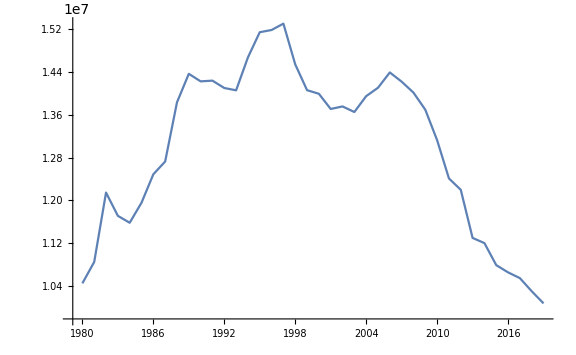

```mathematica
ListLinePlot[letaInAretacije, ImageSize -> Large]
```

Z zgornjega grafa lahko opazimo, da se število aretacij skozi leta zmanjšuje, kar je zelo dobro. Lahko sklepamo, da bo v prihodnje še manj aretacij.

```mathematica
tab=Select[letaInAretacije,#["Arrests"]==Max[letaInAretacije[All,{2}]]&];
tab[All,{1}]
tab[All,{2}]
```

```mathematica
tab2=Select[letaInAretacije,#["Arrests"]==Min[letaInAretacije[All,{2}]]&];
tab2[All,{1}]
tab2[All,{2}]
```

Iz grafa in tabel lahko vidimo, da je bilo največ aretacij lata 1997, kjer je bilo 15.290.920 aretacij, najmanj pa jih je bilo leta 2019, ker je bilo
10.085.207 aretacij.

S pomočjo spodnje funkcije lahko za poljubno leto med 1980 in 2019 vidimo koliko aretacij je bilo.

```mathematica
stAretacijLeto[leto_] := DecimalForm[Total[podatki[Select[#"Years" == leto&],{2}]]]
stAretacijLeto[2000]
```

<|Arrests→13985979.|>

## Aretacije mladoletnih in polnoletnih

Preveril bom število mladoletnih in polnoletnih aretirancev skozi vsa leta.

```mathematica
letniceMlad = podatki[All,{1,11}]
letnicePolno = podatki[All, {1,12}]
```

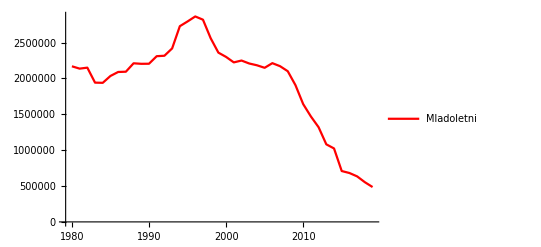

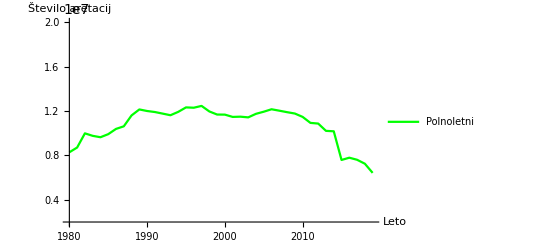

```mathematica
grafMlad = ListLinePlot[letniceMlad, PlotStyle->Red, PlotLegends->{"Mladoletni"}, PlotRange->All,PlotRange->{1980,2019}]
grafPolno = ListLinePlot[letnicePolno,PlotStyle-> Green, PlotLegends->{"Polnoletni"},AxesLabel->{"Leto", "Število aretacij"}, PlotRange->{{1980,2019},{2000000,20000000}}]
```

```mathematica
mladoletniInPolnoletni = DecimalForm[Total[podatki[All,{11,12}]]]
```

<|Under 18→77670691.,18 or over→429303722.|>

Z grafov in spremenljivke “mladoletniInPolnoletni” lahko vidimo, da je mladoletnih manj kot polnoletnih, kar ni presenetljiv podatek. Vidimo tudi, da število tako polnoletnih kot mladoletnih pada, kar je dobro.

## Analiza aretacij glede na raso

```mathematica
belciLeta = podatki[All,{1,3}]
```

```mathematica
crnciLeta = podatki[All,{1,4}]
```

```mathematica
azijciLeta = podatki[All,{1,5}]
```

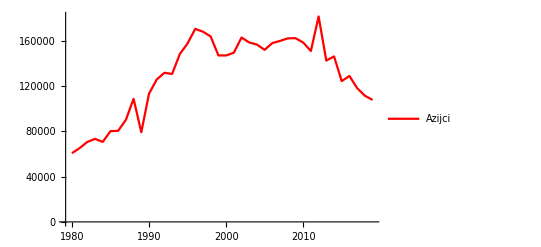

```mathematica
grafA = ListLinePlot[azijciLeta, PlotStyle->Red, PlotLegends->{"Azijci"}, PlotRange->All,PlotRange->{{1980,2019},{50000,20000000}}]
```

```mathematica
grafB =   ListLinePlot[belciLeta,PlotStyle-> Purple, PlotLegends->{"Belci"},AxesLabel->{"Leto"}, PlotRange->{{1980,2019},{2000000,20000000}}]
```

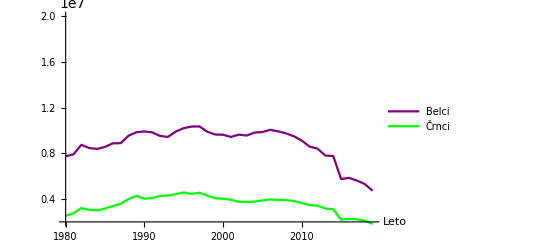

-Graphics-

```mathematica
grafC = ListLinePlot[crnciLeta,PlotStyle-> Green, PlotLegends->{"Črnci"},AxesLabel->{"Leto"}, PlotRange->{{1980,2019},{50000,20000000}}]

 Show[grafB,grafC]
Show[grafA]
```

Na zgorjnih grafih lahko vidimo, da je najmanj aretacij bilo pri azijcih, medtem ko je bilo največ aretacij pri belcih.
Aretacij pri Azijcih je bilo drastično manj kot pri drugima dvema rasama. Azijcev je bilo v zadnjih 40 letih vsako leto manj kot 200.000 aretiranih, medtem ko je bilo pri drugima dvema
rasama bila številka vedno nad 1.000.000


S pomočjo spodnje funkcije lahko za določeno leto in raso vidimo število aretirancev.

```mathematica
stAretacijRasa[year_,rasa_] := podatki[Select[#"Years" == year&]][All,{rasa}]
```

```mathematica
stAretacijRasa[1990,"Asian"]
```

```mathematica
tabela = Dataset[Total[podatki[All,{"White","Black","Asian"}]]]
```

```mathematica
belci=Total[podatki[All,"White"]]
```

3.52459×10^8

```mathematica
vsi=Total[tabela];
```

```mathematica
bel=Interpreter["Percent"][(belci * 100)/vsi]
```

70.4984 %

```mathematica
crni=Total[podatki[All,"Black"]];
```

```mathematica
crn=Interpreter["Percent"][(crni * 100)/vsi]
```

28.4669 %

```mathematica
azijci=Total[podatki[All,"Asian"]];
```

```mathematica
azic=Interpreter["Percent"][(azijci * 100)/vsi]
```

1.03466 %

```mathematica
odstotki=Dataset[{bel,crn,azic}]
```

```mathematica
PieChart[odstotki,ChartLegends-> {"White","Black","Asian"},ChartLabels->{odstotki[1],odstotki[2],odstotki[3]}]
```

-Graphics-

S tortnega diagrama lahko vidimo, da je bilo aretiranih daleč največ belcev, malo manj je bilo črncev, najmanj pa azijcev.

## Analiza vzrokov za aretacije

Za aretacijo je možnih veliko vzrokov. Iz pridobljenih podatkov bom analiziral le nekaj vzrokov zaradi katerih so ljudje bili aretirani.

```mathematica
aretacije = podatki[All,{1,6,7,8,9,10}]
```

Funkcija ‘drogepodatki’ nam vrne število aretacij zaradi uporabe drog, voznjo pod vplivom, napadov, ropov, ter kraje vozil za določeno leto med 1980 in 2019.

```mathematica
drogepodatki[godina_]:=aretacije[Select[#"Years"==godina&],{2,3,4,5,6}]
```

```mathematica
drogepodatki[1985]
```

Preveril bom katerih kršitev je bilo največ v zadnjih 40 letih.

```mathematica
stDrog = Total[podatki[All, "Drug abuse"]]
```

5.43429×10^7

```mathematica
stPijanih = Total[podatki[All, "Driving under influence"]]
```

5.8437×10^7

```mathematica
stNapadov = Total[podatki[All, "Assault"]]
```

5.98376×10^7

```mathematica
stRopov = Total[podatki[All, "Robbery"]]
```

5.14845×10^6

```mathematica
stKrajAvtov = Total[podatki[All, "Vehicle theft"]]
```

5.4672×10^6

Vidimo, da je bilo v ZDA največ ljudi aretiranih zaradi napadov na sočloveka.

## Aplikacija v oblaku

```mathematica
grafAretacij[krsitev_] := ListLinePlot[podatki[All,{"Years",krsitev}], PlotLabel->"Prikaz aretacij zaradi določene kršitve.", AxesLabel->{"Leto","Število kršitev"},PlotStyle->Orange, ImageSize->{800,550}]
```

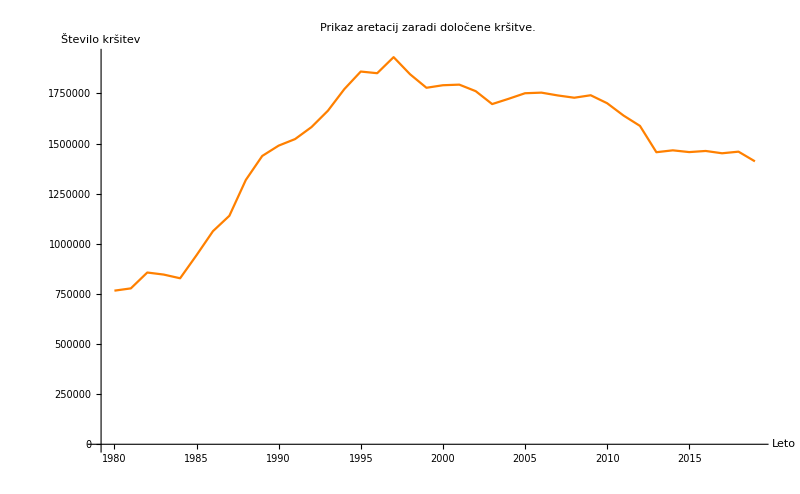

```mathematica
grafAretacij["Assault"]
```

```mathematica
obrazec = FormPage["krsitev"-> "",grafAretacij[#krsitev]&,
AppearanceRules-><|"Title" -> "Graf števila kršitev v odvisnosti od časa.","Description"-> "Vnesite kršitev (izbirate lahko med: Drug abuse, Driving under influence, Assault, Robbery, Vehicle theft)","SubmitLabel" -> "Potrdi"|>]
```

```mathematica
CloudDeploy[obrazec,Permissions->"Public"]
```

Import::jsonhintposandchar: An error occurred near character '!', at line 1:3

$Failed